```mathematica
BlueC=RGBColor[0.2627,0.4313,1];
PurpleC=RGBColor[0.5411,0.0784,0.9607];
RedC=RGBColor[0.60,0.30,0];
```

# Ultrastrong simple coupling

1. The system has two TLSs coupled each to a thermal bath.
2. The energy levels of the two levels are not necessarily resonant
3. An ultrastrong interaction between the two systems mediates the thermal flow from bath to bath.

Here we take the inter-TLS coupling to be ultrastrong. Hence global master equation needs to be used for analysis.

## System Hamiltonians

Identity operator

```mathematica
Id[ve_,ho_]:=ve,ho
```

### Subsystem Hamiltonians

There are two subsystems L and R, each of which are TLSs.

Combined form for the two non-interacting subsystem Hamiltonians

(Ĥ)_sys^0 = (ℏ ω_L)/2 (|e_L><e_L|-|g_L><g_L|) + (ℏ ω_R)/2 (|e_R><e_R|-|g_R><g_R|)

```mathematica
HLSep[veL_,hoL_,veR_,hoR_]:=({{(ℏ Subscript[ω, 1])/2, 0}, {0, -(ℏ Subscript[ω, 1])/2}})[[veL,hoL]]Id[veR,hoR]
HRSep[veL_,hoL_,veR_,hoR_]:=Id[veL,hoL]({{(ℏ Subscript[ω, 2])/2, 0}, {0, -(ℏ Subscript[ω, 2])/2}})[[veR,hoR]]
```

Eigenstates,
|1>	= |e,e>
|2>	= |e,g>
|3>	= |g,e>
|4>	= |g,g>

Eigenstate mapping function, (maps overall state (1 to 4) to subsystem L, R state,

```mathematica
EmapL[i_]:=(i,3+i,4)2+(i,1+i,2)1
EmapR[i_]:=(i,2+i,4)2+(i,1+i,3)1
```

Matrix form of the two subsystem Hamiltonians

```mathematica
HL[ve_,ho_]:=HLSep[EmapL[ve],EmapL[ho],EmapR[ve],EmapR[ho]]
HR[ve_,ho_]:=HRSep[EmapL[ve],EmapL[ho],EmapR[ve],EmapR[ho]]
```

Non-interacting subsystem Hamiltonians as a matrix in the combined system space

```mathematica
Hsys0Matrix = Table[HL[ve,ho]+HR[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[Hsys0Matrix]
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | 0 | 0
0 | 0 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

## Interaction Hamiltonian between the two TLSs

Interaction between the two subsystems are of the form

(Ĥ)_sys^1 = (ℏ γ)/2(σ_+^L ⊗ σ_-^R + σ_-^L ⊗ σ_+^R)
	= (ℏ γ)/2(|e_L><g_L|⊗|g_R><e_R| + |g_L><e_L|⊗|e_R><g_R|)

Considering the above Hamiltonian, we write the interaction between L and M as,

```mathematica
Hint[ve_,ho_]:=(ℏ γ)/2 (KroneckerProduct[({{0, 1}, {0, 0}}),({{0, 0}, {1, 0}})]+KroneckerProduct[({{0, 0}, {1, 0}}),({{0, 1}, {0, 0}})])[[ve,ho]]
```

Interacting system Hamiltonian as a matrix in the combined system space

```mathematica
Hsys1Matrix:=Table[Hint[ve,ho],{ve,1,4},{ho,1,4}];
MatrixForm[Hsys1Matrix]
```

(0 | 0 | 0 | 0
0 | 0 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | 0 | 0
0 | 0 | 0 | 0)

## Combined system Hamiltonian

(Ĥ)_sys = (Ĥ)_sys^0 + (Ĥ)_sys^1

```mathematica
HsysMatrix=Hsys0Matrix+Hsys1Matrix;
MatrixForm[HsysMatrix]
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

### Visualize the energy levels of the combined system

```mathematica
unitassum={ℏ->1};
```

#### Bare energy levels without the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift1[i_]:=i,1 4+i,2 2+i,3 3+i,4 1
```

```mathematica
Hsys0EVal[i_]:=Eigenvalues[Hsys0Matrix][[Shift1[i]]]
Hsys0EVec[i_]:=Eigenvectors[Hsys0Matrix][[Shift1[i]]]

Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

```mathematica
Manipulate[Module[{temp},
temp=Table[Hsys0EVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,unitassum}];
Plot[temp,{t,0,2},PlotLegends->{"|1> = |ee>","|2> = |eg>","|3> = |ge>","|4> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic}]
],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},{{ω2,0.9},0,3}]
```

ReplaceAll::reps: {ω_1→1.1,ω_2→0.9,unitassum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

#### Dressed energy levels with the interaction Hamiltonian

Function for shifting the eigenvalues from Mathematica to our representation

```mathematica
Shift2[i_]:=i,1 2+i,2 4+i,3 3+i,4 1
```

```mathematica
HsysEVal[i_]:=Eigenvalues[HsysMatrix][[Shift2[i]]]
HsysEVec[i_]:=Simplify[Normalize[Eigenvectors[HsysMatrix][[Shift2[i]]]]]

Table[{HsysEVal[i],MatrixForm[HsysEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{-1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2),(0
-(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2))
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

```mathematica
Manipulate[Module[{temp},
temp=Table[HsysEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
{Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic},ImageSize->Medium]
,Table[MatrixForm[HsysEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},{{ω2,0.9},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,0.3}]
```

ReplaceAll::reps: {ω_1→1.1,ω_2→0.9,γ→0.001,unitassum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Strengthening the interaction Hamiltonian (in the ultrastrong region) further separates the middle two energy levels.

#### Resonant coupling (i.e. ω_1=ω_2)

```mathematica
Manipulate[Module[{temp},
temp=Table[HsysEVal[i],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ωs,Subscript[ω, 2]->ωs,γ->γs,unitassum}];
{Plot[temp,{t,0,2},PlotLegends->{"|1_DRE> = |ee>","|2_DRE>","|3_DRE>","|4_DRE> = |gg>"},AxesLabel->{None,"Energy"},PlotRange->{-1.5,1.5},Ticks->{None,Automatic},ImageSize->Medium]
,Table[MatrixForm[HsysEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ωs,Subscript[ω, 2]->ωs,γ->γs,unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ωs,0.9},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,0.3}]
```

ReplaceAll::reps: {ω_1→0.9,ω_2→0.9,γ→0.001,unitassum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

## Representing the system Hamiltonian (Ĥ)_sys in new (dressed) |i_DRE>; i=1,2,3,4 basis

Bare eigensystem (without interaction)

```mathematica
Table[{Hsys0EVal[i],MatrixForm[Hsys0EVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{1/2 ℏ (ω_1-ω_2),(0
1
0
0)},{1/2 ℏ (-ω_1+ω_2),(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

Define 
	Detuning  Δ= (ω_1-ω_2)
	Rabi frequency Ω = √(γ^2+Δ^2)

```mathematica
ΔΩassum={Ω->√(γ^2+Subscript[ω, 1]^2-2 Subscript[ω, 1] Subscript[ω, 2]+Subscript[ω, 2]^2),Δ->Subscript[ω, 1]-Subscript[ω, 2]};
```

Dressed Eigensystem (with interaction)

```mathematica
Table[{HsysEVal[i],MatrixForm[HsysEVec[i]]},{i,1,4}]//.{√(γ^2+Subscript[ω, 1]^2-2 Subscript[ω, 1] Subscript[ω, 2]+Subscript[ω, 2]^2)->Ω,-Subscript[ω, 1]+Subscript[ω, 2]->-Δ,Subscript[ω, 1]-Subscript[ω, 2]->Δ}
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{(Ω ℏ)/2,(0
(Δ+Ω)/(γ √(1+Abs[(Δ+Ω)/γ]^2))
1/(√(1+Abs[(Δ+Ω)/γ]^2))
0)},{-(Ω ℏ)/2,(0
-(-Δ+Ω)/(γ √(1+Abs[(-Δ+Ω)/γ]^2))
1/(√(1+Abs[(-Δ+Ω)/γ]^2))
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

Simplifying,

(0
(Δ+Ω)/(γ √(1+Abs[(Δ+Ω)/γ]^2))
1/(√(1+Abs[(Δ+Ω)/γ]^2))
0)=(0
(Δ+Ω)/(√(γ^2+(Δ+Ω)^2))
γ/(√(γ^2+(Δ+Ω)^2))
0)=1/(√(γ^2+(Ω+Δ)^2))(0
Δ+Ω
γ
0)
(0
-(-Δ+Ω)/(γ √(1+Abs[(-Δ+Ω)/γ]^2))
1/(√(1+Abs[(-Δ+Ω)/γ]^2))
0)=(0
-(Ω-Δ)/(√(γ^2+(Ω-Δ)^2))
γ/(√(γ^2+(Ω-Δ)^2))
0)=1/(√(γ^2+(Ω-Δ)^2))(0
Δ-Ω
γ
0)

```mathematica
HsysEValSimp[i_]:={1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2]),1/2 ℏ Ω,-1/2 ℏ Ω,-1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2])}[[i]]
HsysEVecSimp[i_]:={({{1}, {0}, {0}, {0}}),1/(√(γ^2+(Ω+Δ)^2))({{0}, {Δ+Ω}, {γ}, {0}}),1/(√(γ^2+(Ω-Δ)^2))({{0}, {Δ-Ω}, {γ}, {0}}),({{0}, {0}, {0}, {1}})}[[i]]
```

Diagonalizing the Hamiltonian (Ĥ)_sys on |1_DRE>, |2_DRE>, |3_DRE> and |4_DRE> given above can bring it back to a form without the interaction Hamiltonian but with different ω_1 and ω_2.
	ω_1^DRE=ω_1-Ω/2
	ω_2^DRE=ω_2+Ω/2
Have to be careful because two middle eigenvectors are now mixed states.

### Diagonalizing the system Hamiltonian

```mathematica
HsysEVecMatrix=Table[HsysEVec[i],{i,1,4}];
MatrixForm[HsysEVecMatrix]
```

(1 | 0 | 0 | 0
0 | (ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
0 | -(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
0 | 0 | 0 | 1)

```mathematica
HsysMatrix//MatrixForm
Simplify[(Inverse[HsysEVecMatrix].DiagonalMatrix[Table[HsysEVal[i],{i,1,4}]].HsysEVecMatrix)]//MatrixForm
```

((ℏ ω_1)/2+(ℏ ω_2)/2 | 0 | 0 | 0
0 | (ℏ ω_1)/2-(ℏ ω_2)/2 | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -(ℏ ω_1)/2+(ℏ ω_2)/2 | 0
0 | 0 | 0 | -(ℏ ω_1)/2-(ℏ ω_2)/2)

(1/2 ℏ (ω_1+ω_2) | 0 | 0 | 0
0 | 1/2 ℏ (ω_1-ω_2) | (γ ℏ)/2 | 0
0 | (γ ℏ)/2 | -1/2 ℏ (ω_1-ω_2) | 0
0 | 0 | 0 | -1/2 ℏ (ω_1+ω_2))

The diagonalization is through a unitary transformation U, with U being the eigenvector matrix.

Inverting the diagonalization gives the Hamiltonian in the |1_DRE>, |2_DRE>, |3_DRE> and |4_DRE> basis,

```mathematica
HsysDREMatrix=Simplify[HsysEVecMatrix.HsysMatrix.Inverse[HsysEVecMatrix]];
MatrixForm[HsysDREMatrix]
```

(1/2 ℏ (ω_1+ω_2) | 0 | 0 | 0
0 | 1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2) | 0 | 0
0 | 0 | -1/2 ℏ √(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2) | 0
0 | 0 | 0 | -1/2 ℏ (ω_1+ω_2))

We will work in this basis from now on.

```mathematica
HsysDRESimpMatrix=({{1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2]), 0, 0, 0}, {0, 1/2 ℏ Ω, 0, 0}, {0, 0, -1/2 ℏ Ω, 0}, {0, 0, 0, -1/2 ℏ (Subscript[ω, 1]+Subscript[ω, 2])}});
```

```mathematica
HsysEVecSimpMatrix=Table[HsysEVecSimp[i],{i,1,4}];
```

Verify both eigenvector matrices are physically the same thing

```mathematica
HsysEVecMatrix//MatrixForm
HsysEVecSimpMatrix//MatrixForm
```

(1 | 0 | 0 | 0
0 | (ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(ω_1-ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
0 | -(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/(γ √(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 1/(√(1+Abs[(-ω_1+ω_2+√(γ^2+ω_1^2-2 ω_1 ω_2+ω_2^2))/γ]^2)) | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | (Δ+Ω)/(√(γ^2+(Δ+Ω)^2)) | γ/(√(γ^2+(Δ+Ω)^2)) | 0
0 | (Δ-Ω)/(√(γ^2+(-Δ+Ω)^2)) | γ/(√(γ^2+(-Δ+Ω)^2)) | 0
0 | 0 | 0 | 1)

We will work in this basis from now on,
	with the Hamiltonian

```mathematica
HsysDRESimpMatrix//MatrixForm
```

(1/2 ℏ (ω_1+ω_2) | 0 | 0 | 0
0 | (Ω ℏ)/2 | 0 | 0
0 | 0 | -(Ω ℏ)/2 | 0
0 | 0 | 0 | -1/2 ℏ (ω_1+ω_2))

and eigensystem

```mathematica
Shift3[i_]:=i,1 4+i,2 2+i,3 1+i,4 3
```

```mathematica
HsysDRESSimpEVal[i_]:=Eigenvalues[HsysDRESimpMatrix][[Shift3[i]]]
HsysDRESSimpEVec[i_]:=Simplify[Normalize[Eigenvectors[HsysDRESimpMatrix][[Shift3[i]]]]]

Table[{HsysDRESSimpEVal[i],MatrixForm[HsysDRESSimpEVec[i]]},{i,1,4}]
```

{{1/2 ℏ (ω_1+ω_2),(1
0
0
0)},{(Ω ℏ)/2,(0
1
0
0)},{-(Ω ℏ)/2,(0
0
1
0)},{1/2 ℏ (-ω_1-ω_2),(0
0
0
1)}}

## Pauli matrices

### In z-base representation

|+z>=(1,0)
|-z>=(0,1)

```mathematica
Subscript[σ, axis_][ve_,ho_]:=axis,1({{0, 1}, {1, 0}})[[ve,ho]]+axis,2({{0, -ⅈ}, {ⅈ, 0}})[[ve,ho]]+axis,3({{1, 0}, {0, -1}})[[ve,ho]];
Id[ve_,ho_]:=ve,ho
```

```mathematica
{Table[Subscript[σ, 1][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 2][ve,ho],{ve,1,2},{ho,1,2}],Table[Subscript[σ, 3][ve,ho],{ve,1,2},{ho,1,2}]};
Map[MatrixForm,%,1]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

### In compound system representation

```mathematica
Subscript[σ, P_,axis_][ve_,ho_]:=
P,1(Subscript[σ, axis][EmapL[ve],EmapL[ho]]Id[EmapR[ve],EmapR[ho]])+
P,2(Id[EmapL[ve],EmapL[ho]]Subscript[σ, axis][EmapR[ve],EmapR[ho]])

Subscript[σMatrix, P_,axis_]:=Table[Subscript[σ, P,axis][ve,ho],{ve,1,4},{ho,1,4}]
Subscript[σPMatrix, P_]:=1/2(Subscript[σMatrix, P,1]+ⅈ Subscript[σMatrix, P,2])
Subscript[σMMatrix, P_]:=1/2(Subscript[σMatrix, P,1]-ⅈ Subscript[σMatrix, P,2])
```

```mathematica
{MatrixForm[Subscript[σMatrix, 1,1]],MatrixForm[Subscript[σMatrix, 2,1]]}
```

{(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)}

### In new |i_DRE> dressed system basis

We put the Pauli matrices through the same unitary transformation we used above to convert HtotMatrix to HtotDREMatrix

```mathematica
Subscript[σDREMatrix, P_,axis_]:=HsysEVecSimpMatrix.Subscript[σMatrix, P,axis].Inverse[HsysEVecSimpMatrix]
Subscript[σPDREMatrix, P_]:=HsysEVecSimpMatrix.Subscript[σPMatrix, P].Inverse[HsysEVecSimpMatrix]
Subscript[σMDREMatrix, P_]:=HsysEVecSimpMatrix.Subscript[σMMatrix, P].Inverse[HsysEVecSimpMatrix]
```

```mathematica
{MatrixForm[Subscript[σDREMatrix, 1,1]],MatrixForm[Subscript[σDREMatrix, 2,1]]}
```

{(0 | -((Δ-Ω) √(γ^2+(Δ+Ω)^2))/(2 γ Ω) | ((Δ+Ω) √(γ^2+(-Δ+Ω)^2))/(2 γ Ω) | 0
γ/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | (Δ+Ω)/(√(γ^2+(Δ+Ω)^2))
γ/(√(γ^2+(-Δ+Ω)^2)) | 0 | 0 | (Δ-Ω)/(√(γ^2+(-Δ+Ω)^2))
0 | (√(γ^2+(Δ+Ω)^2))/(2 Ω) | -(√(γ^2+(-Δ+Ω)^2))/(2 Ω) | 0),(0 | (√(γ^2+(Δ+Ω)^2))/(2 Ω) | -(√(γ^2+(-Δ+Ω)^2))/(2 Ω) | 0
(Δ+Ω)/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | γ/(√(γ^2+(Δ+Ω)^2))
(Δ-Ω)/(√(γ^2+(-Δ+Ω)^2)) | 0 | 0 | γ/(√(γ^2+(-Δ+Ω)^2))
0 | -((Δ-Ω) √(γ^2+(Δ+Ω)^2))/(2 γ Ω) | ((Δ+Ω) √(γ^2+(-Δ+Ω)^2))/(2 γ Ω) | 0)}

## Calculating positive transition frequencies

Assumptions on energy levels

```mathematica
ωassum={Subscript[ω, 1]->1.1,Subscript[ω, 2]->0.9,Ω->0.1};
```

Transition frequencies,

```mathematica
ω[m_,n_]:=Simplify[(HsysEValSimp[m]-HsysEValSimp[n])/ℏ]
```

Unique and positive transition frequencies,

```mathematica
ω[i_]:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp1 temp3,0][[i]]
]
ωsize:=Module[{temp1,temp2,temp3},
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
Dimensions[DeleteCases[temp1 temp3,0]][[1]]
]
ωplus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsysEValSimp[m],{m,1,4},{n,m+1,4}]];
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
ωminus[i_]:=Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[Table[HsysEValSimp[m],{m,1,4},{n,m+1,4}]];
temp1=Flatten[Table[ω[m,n],{m,1,4},{n,m+1,4}]];
temp2=temp1/.ωassum;
temp3=MapIndexed[Boole[(Count[Abs[temp2[[1;;#2[[1]]-1]]],Abs[#1]]==0)&&(#1≠0)] &,temp2];
DeleteCases[temp0 temp3,0][[i]]
]
```

```mathematica
Table[ω[i],{i,1,ωsize}]
ωsize
```

{1/2 (-Ω+ω_1+ω_2),1/2 (Ω+ω_1+ω_2),ω_1+ω_2,Ω}

4

## Density Matrix

```mathematica
ρDREMatrix[t_]:=Table[Subscript[ρ, ve,ho][t],{ve,1,4},{ho,1,4}]
```

```mathematica
MatrixForm[ρDREMatrix[t]]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t])

## Thermal interactions with the baths

The two corner two-level systems interact thermally with respective bosonic thermal baths B_L and B_R with temperatures T_L and T_R, and Hamiltonian.

(Ĥ)_bath^P = ℏ ∑_k ω_k (b̂)_k^P†(b̂)_k^P

Interaction Hamiltonian between the thermal bath L or R with the two TLSs is modelled after the Spin-Boson model in the x-component

(Ĥ)_(sys-bath)^P = ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)

Note - Here, P = L, R (or in the simulations P = 1, 2)

### Get projection matrices Π(ϵ)

Assume the energy levels are such that all eigenvalues are non-degenerate. The projection matrix then reads,

Π̂[ϵ_i] = |i><i|

where ϵ_i is the energy of the i^th state (in the dressed basis).

```mathematica
πMatrix[i_]:={({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}}),({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})}[[i]]
```

### Get Lindblad operators A^P(ω)

From Eq. (15) of Optically Controlled Quantum Thermal Gate, we see that, for the above (Ĥ)_(sys-bath)^P interaction Hamiltonian, the Lindblad operators are given by,

(Â)_P[ω] = ∑_(ϵ1-ϵ2=ℏ ω) Π̂[ϵ2].(σ̂)_x^P.Π̂[ϵ1]
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,ϵ_i-ϵ_jΠ̂[ϵ_j].(σ̂)_x^P.Π̂[ϵ_i]

where N is the dimensionality of the system.

```mathematica
Subscript[AMatrix, P_][ωs_]:=Simplify[∑_(i=1)^4 ∑_(j=1)^4 ωs,ω[i,j](πMatrix[j].Subscript[σDREMatrix, P,1].πMatrix[i]),Assumptions->{Ω>0,Subscript[ω, 1]>0,Subscript[ω, 2]>0,Subscript[ω, 1]+Subscript[ω, 2]>3Ω}]
```

Lindbladian terms involve a summation of A^P(ω) terms for positive omega.

```mathematica
Table[MatrixForm[Subscript[AMatrix, 1][ω[i]]],{i,1,ωsize}]
Table[MatrixForm[Subscript[AMatrix, 2][ω[i]]],{i,1,ωsize}]
```

{(0 | 0 | 0 | 0
γ/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -(√(γ^2+(Δ-Ω)^2))/(2 Ω) | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
γ/(√(γ^2+(Δ-Ω)^2)) | 0 | 0 | 0
0 | (√(γ^2+(Δ+Ω)^2))/(2 Ω) | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

{(0 | 0 | 0 | 0
(Δ+Ω)/(√(γ^2+(Δ+Ω)^2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (√(γ^2+(Δ-Ω)^2) (Δ+Ω))/(2 γ Ω) | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
(Δ-Ω)/(√(γ^2+(Δ-Ω)^2)) | 0 | 0 | 0
0 | ((-Δ+Ω) √(γ^2+(Δ+Ω)^2))/(2 γ Ω) | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

Define new quantities η and ν

η = γ/(√(γ^2+(Δ+Ω)^2)) = (√(γ^2+(Δ-Ω)^2))/(2 Ω) = -(Δ-Ω)/(√(γ^2+(Δ-Ω)^2)) = ((-Δ+Ω)√(γ^2+(Δ+Ω)^2))/(2 γ Ω)
ν = γ/(√(γ^2+(Δ-Ω)^2)) = (√(γ^2+(Δ+Ω)^2))/(2 Ω) = (Δ+Ω)/(√(γ^2+(Δ+Ω)^2)) = ((Δ+Ω)√(γ^2+(Δ-Ω)^2))/(2 γ Ω)

```mathematica
ηνassum={η->γ/(√(γ^2+(Δ+Ω)^2)),ν->γ/(√(γ^2+(Δ-Ω)^2))};
```

Verify that the four expressions above for ν and η above are indeed equal,

```mathematica
Manipulate[Module[{temp},{
temp=Table[MatrixForm[Subscript[AMatrix, 1][ω[i]]],{i,1,ωsize}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,Δ->ω1-ω2,Ω->√(γs^2+(ω1-ω2)^2),unitassum}],
temp=Table[MatrixForm[Subscript[AMatrix, 2][ω[i]]],{i,1,ωsize}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,Δ->ω1-ω2,Ω->√(γs^2+(ω1-ω2)^2),unitassum}],
{η,ν}//.Flatten[{ηνassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,Δ->ω1-ω2,Ω->√(γs^2+(ω1-ω2)^2),unitassum}]
}],
Delimiter,Item["Frequencies",Alignment->Center],
{{ω1,1.1},0,3},{{ω2,0.9},0,3},
Delimiter,Item["Interaction strength",Alignment->Center],
{{γs,0.001},0.001,3}]
```

Table::iterb: Iterator {i,1,ωsize} does not have appropriate bounds.

ReplaceAll::reps: {ω_1→1.1,ω_2→0.9,γ→0.001,Δ→0.2,Ω→0.200002,unitassum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Table::iterb: Iterator {i,1,ωsize} does not have appropriate bounds.

ReplaceAll::reps: {ω_1→1.1,ω_2→0.9,γ→0.001,Δ→0.2,Ω→0.200002,unitassum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {ηνassum,ω_1→1.1,ω_2→0.9,γ→0.001,Δ→0.2,Ω→0.200002,unitassum} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Subscript[AMatrixSimp, 1][ω[1]]=({{0, 0, 0, 0}, {η, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, -η, 0}});Subscript[AMatrixSimp, 1][ω[2]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {ν, 0, 0, 0}, {0, ν, 0, 0}});Subscript[AMatrixSimp, 1][ω[3]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});Subscript[AMatrixSimp, 1][ω[4]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Subscript[AMatrixSimp, 2][ω[1]]=({{0, 0, 0, 0}, {ν, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, ν, 0}});Subscript[AMatrixSimp, 2][ω[2]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {-η, 0, 0, 0}, {0, η, 0, 0}});Subscript[AMatrixSimp, 2][ω[3]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});Subscript[AMatrixSimp, 2][ω[4]]=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

### Calculate Lindbladian terms

Linbladian for the Markovian quantum master equation, as given in Eq. (13) of Optically Controlled Quantum Thermal Gate

(ℒ̂)_P[ρ̂] = ∑_(ω>0) (𝒥_P[ω](1+n_P[ω])((Â)_P[ω]ρ̂(Â)_P[ω]†-1/2{(Â)_P[ω]†(Â)_P[ω],ρ̂}) + 𝒥_P[ω] n_P[ω]((Â)_P[ω]†ρ̂(Â)_P[ω]-1/2{(Â)_P[ω](Â)_P[ω]†,ρ̂}))
(Â)_P[ω] = ∑_(ϵ1-ϵ2=ℏ ω) Π̂[ϵ2].(σ̂)_x^P.Π̂[ϵ1]
	  = ∑_(i=1)^N ∑_(j=1)^N ℏ ω,ϵ_i-ϵ_jΠ̂[ϵ_j].(σ̂)_x^P.Π̂[ϵ_i]

```mathematica
Subscript[LinMatrix, P_][ρ_]:=Simplify[∑_(i=1)^ωsize (Subscript[J, P][ω[i]](1+Subscript[NBE, P][ω[i]])(Subscript[AMatrixSimp, P][ω[i]].ρ.Subscript[AMatrixSimp, P][ω[i]]†-1/2(Subscript[AMatrixSimp, P][ω[i]]†.Subscript[AMatrixSimp, P][ω[i]].ρ+ρ.Subscript[AMatrixSimp, P][ω[i]]†.Subscript[AMatrixSimp, P][ω[i]]))+Subscript[J, P][ω[i]]Subscript[NBE, P][ω[i]](Subscript[AMatrixSimp, P][ω[i]]†.ρ.Subscript[AMatrixSimp, P][ω[i]]-1/2(Subscript[AMatrixSimp, P][ω[i]].Subscript[AMatrixSimp, P][ω[i]]†.ρ+ρ.Subscript[AMatrixSimp, P][ω[i]].Subscript[AMatrixSimp, P][ω[i]]†))),Assumptions->{η>0,ν>0}]
```

Net thermal decaying rate Τ_P[i,j] from state | i > to state | j > while releasing energy to reservoir P. Note i > j.
Τs_P[i,j] is used due to variable naming issues.

Γ_(j,k)^P = 𝒥_P[ω_(j,k)]((1+n_P[ω_(j,k)])ρ_(j,j)[t]-n_P[ω_(j,k)]ρ_(k,k)[t])

```mathematica
Subscript[Τs, P_][i_,j_]:=Subscript[J, P][ω[i,j]](1+Subscript[NBE, P][ω[i,j]])Subscript[ρ, i,i][t]-Subscript[J, P][ω[i,j]]Subscript[NBE, P][ω[i,j]]Subscript[ρ, j,j][t]
```

Mathematica function for arithmetically proper replacements,

```mathematica
ReplaceArithmetically[expr_,orig_,repl_]:=
Module[{f},
(*Actual replacement function, but it is not Listable*)
f[exprs_,origs_,repls_]:=Module[{q,r},
{q,r}=PolynomialReduce[exprs,origs,{}];
q.repls+r
];
(*Construct for making the function Listable in only the first argument*)
Function[t,f[t,orig,repl],{Listable}][expr]
]
```

```mathematica
ReplaceArithmetically[Subscript[LinMatrix, 1][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],{η^2,ν^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Table[J[ ω[i]],{i,1,ωsize}]]&]&];
MatrixForm[%]
ReplaceArithmetically[Subscript[LinMatrix, 2][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],{η^2,ν^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Table[J[ ω[i]],{i,1,ωsize}]]&]&];
MatrixForm[%]
```

(-η^2 Τ_1[1,2]-ν^2 Τ_1[1,3] | η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,2)[t]+ν^2 ((-J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]+J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t]) | ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,3)[t]+η^2 ((-J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t]) | η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,4)[t]+ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,4)[t]
η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(2,1)[t]+ν^2 ((-J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]+J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t]) | η^2 Τ_1[1,2]-ν^2 Τ_1[2,4] | η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(2,3)[t]+ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,3)[t] | ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,4)[t]+η^2 ((-J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t])
ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(3,1)[t]+η^2 ((-J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t]) | η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,2)[t]+ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(3,2)[t] | ν^2 Τ_1[1,3]-η^2 Τ_1[3,4] | η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,4)[t]+ν^2 ((J_1[1/2 (Ω+ω_1+ω_2)]+J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t])
η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(4,1)[t]+ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(4,1)[t] | ν^2 (-1/2 J_1[1/2 (Ω+ω_1+ω_2)]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(4,2)[t]+η^2 ((-J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t]) | η^2 (-1/2 J_1[1/2 (-Ω+ω_1+ω_2)]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(4,3)[t]+ν^2 ((J_1[1/2 (Ω+ω_1+ω_2)]+J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t]) | ν^2 Τ_1[2,4]+η^2 Τ_1[3,4])

(-ν^2 Τ_2[1,2]-η^2 Τ_2[1,3] | ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,2)[t]+η^2 ((-J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t]) | η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,3)[t]+ν^2 ((-J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]+J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t]) | ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,4)[t]+η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,4)[t]
ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(2,1)[t]+η^2 ((-J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t]) | ν^2 Τ_2[1,2]-η^2 Τ_2[2,4] | ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(2,3)[t]+η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,3)[t] | η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,4)[t]+ν^2 ((J_2[1/2 (-Ω+ω_1+ω_2)]+J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t])
η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(3,1)[t]+ν^2 ((-J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]+J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t]) | ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,2)[t]+η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(3,2)[t] | η^2 Τ_2[1,3]-ν^2 Τ_2[3,4] | ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,4)[t]+η^2 ((-J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t])
ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(4,1)[t]+η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(4,1)[t] | η^2 (-1/2 J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(4,2)[t]+ν^2 ((J_2[1/2 (-Ω+ω_1+ω_2)]+J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t]) | ν^2 (-1/2 J_2[1/2 (-Ω+ω_1+ω_2)]-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(4,3)[t]+η^2 ((-J_2[1/2 (Ω+ω_1+ω_2)]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t]) | η^2 Τ_2[2,4]+ν^2 Τ_2[3,4])

## Defining the interaction picture

The total Hamiltonian is now given by,

Ĥ = (Ĥ)_sys^0 + (Ĥ)_sys^1 + ∑_(P=L,R) (Ĥ)_bath^P + ∑_(P=L,R) (Ĥ)_(sys-bath)^P 
  = (Ĥ)_sys + ∑_(P=L,R) (Ĥ)_bath^P + ∑_(P=L,R) (Ĥ)_(sys-bath)^P 
  
(Ĥ)_sys^0 = (ℏ ω_L)/2 (|e_L><e_L|-|g_L><g_L|) + (ℏ ω_R)/2 (|e_R><e_R|-|g_R><g_R|)
(Ĥ)_sys^1 = (ℏ γ)/2(|e_L><g_L|⊗|g_R><e_R| + |g_L><e_L|⊗|e_R><g_R|)
(Ĥ)_(sys-bath)^P = ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)
(Ĥ)_bath^P = ℏ ∑_k ω_k (b̂)_k^P†(b̂)_k^P

We work in dressed state basis, hence (Ĥ)_sys is diagonal.

Use the interaction picture defined on

(Ĥ)_0 = (Ĥ)_sys + ∑_(P=L,R) (Ĥ)_bath^P
(Ĥ)_1 = ∑_(P=L,R) (Ĥ)_(sys-bath)^P

which gives the interaction picture Hamiltonian as

(Ĥ)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_0 t].(Ĥ)_1.MatrixExp[-ⅈ/ℏ(Ĥ)_0 t]
		=∑_(P=L,R) MatrixExp[+ⅈ/ℏ((Ĥ)_sys + ∑_(P=L,R) (Ĥ)_bath^P)t].(Ĥ)_(sys-bath)^P.MatrixExp[-ⅈ/ℏ((Ĥ)_sys + ∑_(P=L,R) (Ĥ)_bath^P)t]
		=∑_(P=L,R) MatrixExp[+ⅈ/ℏ((Ĥ)_sys +∑_(P=L,R) (Ĥ)_bath^P)t].(ℏ σ_X^P∑_k g_k((b̂)_k^P+(b̂)_k^P†)).MatrixExp[-ⅈ/ℏ((Ĥ)_sys +∑_(P=L,R) (Ĥ)_bath^P)t]
		=∑_(P=L,R) ℏ(MatrixExp[+ⅈ/ℏ(Ĥ)_sys t].σ_X^P.MatrixExp[-ⅈ/ℏ(Ĥ)_sys t])(MatrixExp[+ⅈ/ℏ(∑_(P=L,R) (Ĥ)_bath^P)t].(∑_k g_k((b̂)_k^P+(b̂)_k^P†)).MatrixExp[+ⅈ/ℏ(∑_(P=L,R) (Ĥ)_bath^P)t])
		=∑_(P=L,R) ℏσ_X^P[t](∑_k g_k((b̂)_k^P[t]+(b̂)_k^P†[t]))
		=∑_(P=L,R) (Ĥ)_(sys-bath,INT)^P[t]
		
(Ĥ)_(sys-bath,INT)^P[t] = MatrixExp[+ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t].(Ĥ)_(sys-bath)^P.MatrixExp[-ⅈ/ℏ((Ĥ)_sys^0+∑_(P=L,R) (Ĥ)_bath^P)t]
			  = ℏσ_X^P[t](∑_k g_k((b̂)_k^P[t]+(b̂)_k^P†[t]))

Here the part with the (Ĥ)_(sys-bath,INT)^P is dealt with by the Lindblad terms.

## Quantum Markovian master equation

Since we consider the full Hamiltonian when deriving the Lindblad operators (i.e., we are working in the dressed state basis), we only need to consider the two dissipation terms.

∂_t (ρ̂)_INT[t]  = (ℒ̂)_L[(ρ̂)_INT[t] ] + (ℒ̂)_R[(ρ̂)_INT[t] ]

Ohmic bath spectral density,

```mathematica
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

Right hand side of the Markovian quantum master equation (in interaction picture),

```mathematica
RHS=Subscript[LinMatrix, 1][ρDREMatrix[t]]+Subscript[LinMatrix, 2][ρDREMatrix[t]];
MatrixForm[%]
```

(-η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(2,2)[t])-ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(2,2)[t])-ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(3,3)[t])-η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(3,3)[t]) | -1/2 η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,2)[t]-1/2 ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,2)[t]-ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t])-η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]+NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t]) | -1/2 ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,3)[t]-1/2 η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,3)[t]-η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]+NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t])-ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t]) | -1/2 (η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)])+ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)])) ρ_(1,4)[t]-1/2 (ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)])+η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(1,4)[t]
-1/2 η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(2,1)[t]-1/2 ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(2,1)[t]-ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t])-η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]+NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t]) | η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(2,2)[t])+ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(2,2)[t])-ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,2)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(4,4)[t])-η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,2)[t]-NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(4,4)[t]) | -1/2 (η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)])+ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)])) ρ_(2,3)[t]-1/2 (ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)])+η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(2,3)[t] | -1/2 ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,4)[t]-1/2 η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,4)[t]-η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]+NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t])+ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t])
-1/2 ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(3,1)[t]-1/2 η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(3,1)[t]-η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]+NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t])-ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t]) | -1/2 (η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)])+ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)])) ρ_(3,2)[t]-1/2 (ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)])+η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(3,2)[t] | ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(3,3)[t])+η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,1)[t]-NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(3,3)[t])-η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,3)[t]-NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(4,4)[t])-ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,3)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(4,4)[t]) | -1/2 η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,4)[t]-1/2 ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,4)[t]+ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t])-η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]+NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t])
-1/2 (η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)])+ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)])) ρ_(4,1)[t]-1/2 (ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)])+η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(4,1)[t] | -1/2 ν^2 J_1[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(4,2)[t]-1/2 η^2 J_2[1/2 (Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(4,2)[t]-η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]+NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t])+ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t]) | -1/2 η^2 J_1[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(4,3)[t]-1/2 ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] (1+2 NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(4,3)[t]+ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t])-η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]+NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t]) | η^2 J_1[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,3)[t]-NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(4,4)[t])+ν^2 J_1[1/2 (Ω+ω_1+ω_2)] ((1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,2)[t]-NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(4,4)[t])+ν^2 J_2[1/2 (-Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,3)[t]-NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(4,4)[t])+η^2 J_2[1/2 (Ω+ω_1+ω_2)] ((1+NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,2)[t]-NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(4,4)[t]))

```mathematica
ReplaceArithmetically[RHS,
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[Expand[%],{η^2,ν^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Flatten[Table[Subscript[J, P][ ω[i]],{i,1,ωsize},{P,1,2}]]]&]&];
MatrixForm[%]
```

(ν^2 (-Τ_1[1,3]-Τ_2[1,2])+η^2 (-Τ_1[1,2]-Τ_2[1,3]) | ν^2 ((J_1[1/2 (Ω+ω_1+ω_2)] (-1-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(1,2)[t]+J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t])+η^2 ((J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(1,2)[t]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(3,4)[t]) | η^2 ((J_1[1/2 (-Ω+ω_1+ω_2)] (-1-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(1,3)[t]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t])+ν^2 ((J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(1,3)[t]+J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(2,4)[t]) | ν^2 (J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(1,4)[t]+η^2 (J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(1,4)[t]
ν^2 ((J_1[1/2 (Ω+ω_1+ω_2)] (-1-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(2,1)[t]+J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t])+η^2 ((J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(2,1)[t]-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)] ρ_(4,3)[t]) | ν^2 (-Τ_1[2,4]+Τ_2[1,2])+η^2 (Τ_1[1,2]-Τ_2[2,4]) | ν^2 (J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(2,3)[t]+η^2 (J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(2,3)[t] | ν^2 (J_2[1/2 (-Ω+ω_1+ω_2)] (1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]+(J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(2,4)[t])+η^2 (J_1[1/2 (-Ω+ω_1+ω_2)] (-1-NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(1,3)[t]+(-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(2,4)[t])
η^2 ((J_1[1/2 (-Ω+ω_1+ω_2)] (-1-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(3,1)[t]-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t])+ν^2 ((J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(3,1)[t]+J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)] ρ_(4,2)[t]) | ν^2 (J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(3,2)[t]+η^2 (J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(3,2)[t] | η^2 (-Τ_1[3,4]+Τ_2[1,3])+ν^2 (Τ_1[1,3]-Τ_2[3,4]) | ν^2 (J_1[1/2 (Ω+ω_1+ω_2)] (1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]+(-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(3,4)[t])+η^2 (J_2[1/2 (Ω+ω_1+ω_2)] (-1-NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(1,2)[t]+(J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(3,4)[t])
ν^2 (J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(4,1)[t]+η^2 (J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(4,1)[t] | ν^2 (J_2[1/2 (-Ω+ω_1+ω_2)] (1+NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]+(J_1[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (Ω+ω_1+ω_2)])-J_2[1/2 (-Ω+ω_1+ω_2)] NBE_2[1/2 (-Ω+ω_1+ω_2)]) ρ_(4,2)[t])+η^2 (J_1[1/2 (-Ω+ω_1+ω_2)] (-1-NBE_1[1/2 (-Ω+ω_1+ω_2)]) ρ_(3,1)[t]+(-J_1[1/2 (-Ω+ω_1+ω_2)] NBE_1[1/2 (-Ω+ω_1+ω_2)]+J_2[1/2 (Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (Ω+ω_1+ω_2)])) ρ_(4,2)[t]) | ν^2 (J_1[1/2 (Ω+ω_1+ω_2)] (1+NBE_1[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]+(-J_1[1/2 (Ω+ω_1+ω_2)] NBE_1[1/2 (Ω+ω_1+ω_2)]+J_2[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_2[1/2 (-Ω+ω_1+ω_2)])) ρ_(4,3)[t])+η^2 (J_2[1/2 (Ω+ω_1+ω_2)] (-1-NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(2,1)[t]+(J_1[1/2 (-Ω+ω_1+ω_2)] (-1/2-NBE_1[1/2 (-Ω+ω_1+ω_2)])-J_2[1/2 (Ω+ω_1+ω_2)] NBE_2[1/2 (Ω+ω_1+ω_2)]) ρ_(4,3)[t]) | η^2 (Τ_1[3,4]+Τ_2[2,4])+ν^2 (Τ_1[2,4]+Τ_2[3,4]))

Left hand side of the Markovian quantum master equation,

```mathematica
LHS=D[ρDREMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t])

Markovian quantum master equation for a general density matrix,

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal];
```

```mathematica
Table[J[ ω[i]],{i,1,ωsize}];
Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]];
sol=ApplySides[Collect[Expand[#],{η^2,ν^2},Collect[#,Flatten[Table[Subscript[ρ, i,j][t],{i,1,4},{j,1,4}]],Collect[#,Table[J[ ω[i]],{i,1,ωsize}]]&]&]&,sol];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;5]];
soloffdiag=Delete[sol,Table[{1+5i},{i,0,3}]];
```

Diagonals of the Markovian quantum master equation simplified to transition rates,

```mathematica
soldiagtran=ApplySides[
ReplaceArithmetically[Simplify[#],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
]&,soldiag]
```

{ρ_(1,1)'[t]==-η^2 Τ_1[1,2]-ν^2 Τ_1[1,3]-ν^2 Τ_2[1,2]-η^2 Τ_2[1,3],ρ_(2,2)'[t]==η^2 Τ_1[1,2]-ν^2 Τ_1[2,4]+ν^2 Τ_2[1,2]-η^2 Τ_2[2,4],ρ_(3,3)'[t]==ν^2 Τ_1[1,3]-η^2 Τ_1[3,4]+η^2 Τ_2[1,3]-ν^2 Τ_2[3,4],ρ_(4,4)'[t]==ν^2 Τ_1[2,4]+η^2 Τ_1[3,4]+η^2 Τ_2[2,4]+ν^2 Τ_2[3,4]}

## Dynamical heat flows

Thermal distributions in the environments (Bose Einstein distribution),

```mathematica
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

```mathematica
Manipulate[Plot[{Subscript[NBE, 1][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 1]->T1},Subscript[NBE, 2][ω]//.{NBEassum,k-> 1,ℏ->1,Subscript[T, 2]->T2}},{ω,0,10 0.2},PlotRange-> {0,2},PlotLegends->{"L","R"},AxesLabel->{"ω","P[ω]"}]
,{{T1,0.2},0.01,1},{{T2,0.1},0.01,1}]
```

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1.,ℏ→1.,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {NBEassum,k→1,ℏ→1,T_1→0.2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

### Characterizing thermal flows

Use the first law of thermodynamics, the rate of change of internal energy of the system is equal to the energy inflows

∂_t <(Ĥ)_sys> = ∑_(P=L,R) J_P[t]

From definition of expected values,

<(Ĥ)_sys> = Tr[(Ĥ)_sys ρ̂[t]] = Tr[(Ĥ)_sys.MatrixExp[-ⅈ/ℏ(Ĥ)_sys t].(ρ̂)_INT[t].MatrixExp[+ⅈ/ℏ(Ĥ)_sys t]]
	= Tr[MatrixExp[+ⅈ/ℏ(Ĥ)_sys t].(Ĥ)_sys.MatrixExp[-ⅈ/ℏ(Ĥ)_sys t].(ρ̂)_INT[t]]
	= Tr[(Ĥ)_sys.(ρ̂)_INT[t]]

where we used

(ρ̂)_INT[t] = MatrixExp[+ⅈ/ℏ(Ĥ)_sys t].ρ̂[t].MatrixExp[-ⅈ/ℏ(Ĥ)_sys t]

Substituting the above expression,

∂_t <(Ĥ)_sys> = ∂_t Tr[(Ĥ)_sys.(ρ̂)_INT[t]]
		= Tr[(Ĥ)_sys.∂_t (ρ̂)_INT[t]]
		= Tr[(Ĥ)_sys.((ℒ̂)_L[(ρ̂)_INT[t]] + (ℒ̂)_R[(ρ̂)_INT[t]])]
		=∑_(P=L,R) Tr[(Ĥ)_sys.(ℒ̂)_P[(ρ̂)_INT[t]]]

∑_(P=L,R) J_P[t] = ∑_(P=L,R) Tr[(Ĥ)_sys.(ℒ̂)_P[(ρ̂)_INT[t]]]

Comparing similar terms on both sides, (see Eq. (19) of Optically Controlled Quantum Thermal Gate)

J_P[t] = Tr[(Ĥ)_sys.(ℒ̂)_P[(ρ̂)_INT[t]]]

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Tr[Subscript[LinMatrix, P][ρ].HsysDRESimpMatrix]
```

```mathematica
ReplaceArithmetically[Subscript[EngyFlowIn, 1][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[%,{η^2,ν^2},Collect[#,Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]]&]

ReplaceArithmetically[Subscript[EngyFlowIn, 2][ρDREMatrix[t]],
Flatten[Table[Subscript[Τs, P][i,j],{P,1,2},{i,1,4},{j,1,4}]],
Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]
];
Collect[%,{η^2,ν^2},Collect[#,Flatten[Table[Subscript[Τ, P][i,j],{P,1,2},{i,1,4},{j,1,4}]]]&]
```

ν^2 ((-(Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_1[1,3]+(-(Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_1[2,4])+η^2 (((Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_1[1,2]+((Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_1[3,4])

η^2 ((-(Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_2[1,3]+(-(Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_2[2,4])+ν^2 (((Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_2[1,2]+((Ω ℏ)/2-(ℏ ω_1)/2-(ℏ ω_2)/2) Τ_2[3,4])

## On unit conversions

To resolve the natural units to SI units, we use the relationship,
Energy = ℏ ω = k_B T
In the natural units case, we have chosen Ts to be an order of magnitude lower than the largest ωs.

In SI units, T'_H = 400, in natural units, T_H=0.2.
This gives a ratio of T'_H/T_H=2000.

Temperature conversion, T'=2000 T

Frequency conversion,  ω'=(2000 k_B)/ℏ ω, Ω'=(2000 k_B)/ℏ Ω

Time conversion,  t'=ℏ/(2000 k_B)t

Transition rates conversion, Τ'=(2000 k_B)/ℏ Τ

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Note - When using SI units, due to frequencies and energies being in widely different orders of magnitudes, there may be numerical errors in calculations. Hence it is always advisable to confirm simulation results with natural unit simulations.

## Density matrix, transition rate and energy flow evolution with time

Assumptions on the temperatures of the baths, TLS energy levels, and TLS interaction strengths,

```mathematica
Tassum={Subscript[T, 1]-> 0.2 Tconv,Subscript[T, 2]-> 0.02 Tconv,Subscript[ω, 1]->1.1 ωconv,Subscript[ω, 2]->0.9 ωconv,Subscript[κ, 1]-> 0.01,Subscript[κ, 2]->0.01};
```

Assumption on the strength of the L-R interaction

```mathematica
γassum={γ->0.001 ωconv};
```

```mathematica
γassum={γ->0.3ωconv};
```

```mathematica
γassum={γ->1ωconv};
```

System energy matrix under above assumptions,

```mathematica
{MatrixForm[HsysMatrix//.Flatten[{Tassum,unitassum,γassum}]],
MatrixForm[HsysDREMatrix//.Flatten[{Tassum,unitassum,γassum}]]}
```

{(1. | 0 | 0 | 0
0 | 0.1 | 1/2 | 0
0 | 1/2 | -0.1 | 0
0 | 0 | 0 | -1.),(1. | 0 | 0 | 0
0 | 0.509902 | 0 | 0
0 | 0 | -0.509902 | 0
0 | 0 | 0 | -1.)}

Numerical solution of the dynamics, with the initial condition that all density matrix elements except the first are zero.

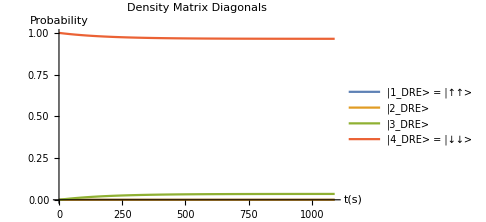

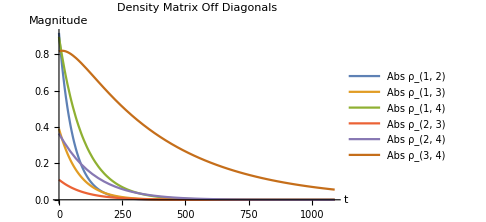
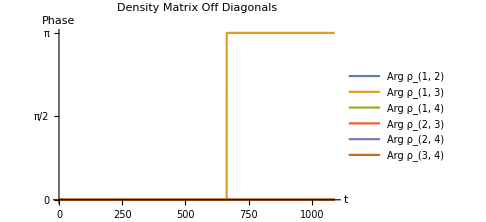

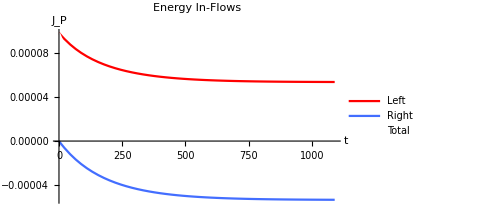

```mathematica
tmax=(1200/Subscript[ω, 1])//.Flatten[{unitassum,Tassum}];

dynamics=NDSolve[
Flatten[{sol//.Flatten[{ΔΩassum,ηνassum,γassum,NBEassum,unitassum,Tassum,Jassum}],Table[Subscript[ρ, i,j][0]==i,j i,4 1+∑_(k=2)^4 ∑_(l=1)^(k-1) (i,k j,l RandomReal[]+j,k i,l RandomReal[]),{i,1,4},{j,1,4}]}]
,Flatten[Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]],{t,0,tmax}
];

Flatten[{Table[Subscript[ρ, i,i][t],{i,1,4}]}/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel->  Style["Density Matrix Diagonals"],
	PlotRange-> {0.0,1},
	AxesLabel->{Style["t(s)"],Style["Probability"]}, 
	PlotLegends->{
		Style["|1_DRE> = |↑↑> "],
		Style["|2_DRE>"],
		Style["|3_DRE>"],
		Style["|4_DRE> = |↓↓> "]}]

plot1=Flatten[{Abs[Subscript[ρ, 1,2][t]],Abs[Subscript[ρ, 1,3][t]],Abs[Subscript[ρ, 1,4][t]],Abs[Subscript[ρ, 2,3][t]],Abs[Subscript[ρ, 2,4][t]],Abs[Subscript[ρ, 3,4][t]]}/.dynamics];
plot2=Flatten[{Arg[Subscript[ρ, 1,2][t]],Arg[Subscript[ρ, 1,3][t]],Arg[Subscript[ρ, 1,4][t]],Arg[Subscript[ρ, 2,3][t]],Arg[Subscript[ρ, 2,4][t]],Arg[Subscript[ρ, 3,4][t]]}/.dynamics];
{Plot[plot1,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange-> Full,
	AxesLabel->{Style["t"],Style["Magnitude"]}, 
	PlotLegends->{
		Style["Abs ρ_(1, 2)"],
		Style["Abs ρ_(1, 3)"],
		Style["Abs ρ_(1, 4)"],
		Style["Abs ρ_(2, 3)"],
		Style["Abs ρ_(2, 4)"],
		Style["Abs ρ_(3, 4)"]}],
Plot[plot2,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Density Matrix Off Diagonals"],
	PlotRange->Full,
	AxesLabel->{"t","Phase"}, 
	Ticks->{Automatic,{0,π/2,π}},
	PlotLegends->{
		Style["Arg ρ_(1, 2)"],
		Style["Arg ρ_(1, 3)"],
		Style["Arg ρ_(1, 4)"],
		Style["Arg ρ_(2, 3)"],
		Style["Arg ρ_(2, 4)"],
		Style["Arg ρ_(3, 4)"]}]}

Flatten[{Subscript[EngyFlowIn, 1][ρDREMatrix[t]],Subscript[EngyFlowIn, 2][ρDREMatrix[t]],Subscript[EngyFlowIn, 1][ρDREMatrix[t]]+Subscript[EngyFlowIn, 2][ρDREMatrix[t]]}//.Flatten[{ΔΩassum,ηνassum,γassum,NBEassum,unitassum,Tassum,Jassum}]/.dynamics];
Plot[%,{t,0,tmax},
	ImageSize->Medium,
	PlotLabel-> Style["Energy In-Flows"],
	AxesLabel->{"t","J_P"},
	PlotLegends->{"Left ","Right","Total"},
	PlotStyle->{Red,BlueC,{White,Dashed}}]
```

## Density matrix, transition rate and energy flow at equilibrium

Energy flows conversion, J'=ℏ(2000 k_B)/ℏ(2000 k_B)/ℏ J=(2000 k_B)^2/ℏ J

Unit conversion factors for SI units,

```mathematica
unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};
```

```mathematica
Tconv=300/0.2;
ωconv=(Tconv k)/ℏ/.unitassum;
tconv=ℏ/(Tconv k)/.unitassum;
Τconv=(Tconv k)/ℏ/.unitassum;
Econv=(Tconv k)^2/ℏ/.unitassum;
```

Unit conversion factors for natural units,

```mathematica
unitassum = {k-> 1,ℏ->1};
```

```mathematica
Tconv=1;
ωconv=1;
tconv=1;
Τconv=1;
Econv=1;
```

Function for density matrix elements, transition rates and energy flows,

```mathematica
varFunc[T1_,T2_,κ1_,κ2_,ω1_,ω2_,γs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{unitassum,Jassum,NBEassum,ΔΩassum,ηνassum,Subscript[T, 1]->T1,Subscript[T, 2]->T2,Subscript[κ, 1]->κ1,Subscript[κ, 2]->κ2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]->0,Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j]},1==∑_(i=1)^4 Subscript[ρ, i,i]}];
temp3=Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]]]];
Re[{
Flatten[Table[Subscript[ρ, i,i],{i,1,4}]]/.temp3,
Flatten[{
η^2 Subscript[Τs, 1][1,2],ν^2 Subscript[Τs, 1][1,3],ν^2 Subscript[Τs, 1][2,4],η^2 Subscript[Τs, 1][3,4],
ν^2 Subscript[Τs, 2][1,2],η^2 Subscript[Τs, 2][1,3],η^2 Subscript[Τs, 2][2,4],ν^2 Subscript[Τs, 2][3,4]
}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3],
Flatten[{
Subscript[EngyFlowIn, 1][ρDREMatrix[t]],Subscript[EngyFlowIn, 2][ρDREMatrix[t]]
}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3],
Table[Subscript[ρ, i,j],{i,1,4},{j,1,4}]//.temp3
}]
]
```

Test function

```mathematica
varFunc[0.2,0.02,1,1,1.1,0.9,0.1,unitassum]
```

{{2.2863×10^-6,0.00363438,0.000626394,0.995737},{-1.92349×10^-6,-1.34179×10^-7,-0.000213295,-0.000526992,1.92349×10^-6,1.34179×10^-7,0.000213295,0.000526992},{0.000707072,-0.000707072},{{2.2863×10^-6,0.,0.,0.},{0.,0.00363438,0.,0.},{0.,0.,0.000626394,0.},{0.,0.,0.,0.995737}}}

Function for drawing a state flow diagram,

```mathematica
DrawFlowGraph[label_,posx_,posy_,nodes_,rates_,ratecolors_,ratesF_,ratecolorsF_,title_,maxrate_]:=Module[{pos,psize},
psize=Dimensions[label][[1]];
pos[i_]:={posx[[i]],posy[[i]]};
Graphics[Flatten[{
{Thickness[0.0001],Arrowheads[0.03],Black,Arrow[{{1.15Min[posx],1.2Min[posy]},{1.15Min[posx],1.1Max[posy]}}]},Black,{Text[Style["Energy",FontSize->13.6,FontFamily->"Times New Roman"],{1.0Min[posx]-0.03,1.15Max[posy]}],Text[Style[title,FontSize->13.6,FontFamily->"Times New Roman"],{0,1.57Min[posy]}]},

Table[{Opacity[1],Thick,RGBColor[0.55,0.55,0.55],Disk[pos[i],0.01+0.22 √nodes[[i]]]},{i,1,psize}],
Table[
	If[rates[[i,j]]≠0 ,
		If[ ratesF[[i,j]]≠0,
			If[Abs[rates[[i,j]]]>Abs[ratesF[[i,j]]],
				{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			,
				{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
				ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]],
				Opacity[1],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
				ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
			]
		,
			{Opacity[0.8],Thickness[0.003+Abs[rates[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[rates[[i,j]]]/maxrate],
			ratecolors[[i,j]],If[rates[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		]
	,
		If[ ratesF[[i,j]]≠0,
			{Opacity[0.8],Thickness[0.003+Abs[ratesF[[i,j]]]/maxrate],Arrowheads[0.04+3Abs[ratesF[[i,j]]]/maxrate],
			ratecolorsF[[i,j]],If[ratesF[[i,j]]>0,Arrow[{pos[i],pos[j]}],Arrow[{pos[j],pos[i]}]]}
		, Nothing]
	]
,{i,1,psize-1},{j,i+1,psize}],
Table[{Opacity[1],Black,Text[Style[label[[i]],FontSize->12],{posx[[i]]+{0,0.04,0,0.06,0.04,0,0.04,0}[[i]],posy[[i]]+{0.045,0.08,-0.05,-0.06,0.06,-0.05,-0.08,0.045}[[i]]}]},{i,1,psize}]

}], ImageSize->Medium]
]

DrawFunc[T1_,T2_,ω1_,ω2_,γs_,title_,maxrate_,var_]:=Module[{label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,temp0},temp0=Flatten[{Jassum,NBEassum,k->1,κ->1,Subscript[T, 1]-> T1,Subscript[T, 2]-> T2,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2}];label={"|1_DRE>=|↑↑>","|2_DRE>","|3_DRE>","|4_DRE>=|↓↓>"};posx={0,-0.4,0.4,0};posy=Diagonal[HsysDREMatrix/(ℏ ωconv)/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}]];nodes=var[[1]];rates=({{0, var[[2]][[1]], var[[2]][[2]], 0}, {0, 0, 0, var[[2]][[3]]}, {0, 0, 0, var[[2]][[4]]}, {0, 0, 0, 0}});
ratesF=({{0, var[[2]][[5]], var[[2]][[6]], 0}, {0, 0, 0, var[[2]][[7]]}, {0, 0, 0, var[[2]][[8]]}, {0, 0, 0, 0}});ratecolors=({{0, Red, RedC, 0}, {0, 0, 0, RedC}, {0, 0, 0, Red}, {0, 0, 0, 0}});
ratecolorsF=({{0, BlueC, Blue, 0}, {0, 0, 0, Blue}, {0, 0, 0, BlueC}, {0, 0, 0, 0}});
DrawFlowGraph[label,posx,posy,nodes,rates,ratecolors,ratesF,ratecolorsF,title,maxrate]
]
```

Steady-state energy flows, transition rates, density matrix diagonals and energy eigenvalues, plotted for dynamically changeable bath, and system parameters,

```mathematica
Manipulate[Module[{temp1,temp2,temp3,temp4,ηs,νs,Δs,Ωs},
temp1=varFunc[T1,T2,κ1,κ2,ω1,ω2,γs,unitassum];
temp2=Table[HsysEVal[i],{i,1,4}]/ℏ/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
temp3=Inverse[HsysEVecMatrix].temp1[[4]].HsysEVecMatrix/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}];
temp4=temp1[[4]];
Δs=Δ//.Flatten[{ΔΩassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
Ωs=Ω//.Flatten[{ΔΩassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
ηs=η//.Flatten[{ΔΩassum,ηνassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
νs=ν//.Flatten[{ΔΩassum,ηνassum,Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs}];
{
Plot[temp2,{t,0,2},
ImageSize->Medium,
PlotLegends->{"|1_DRE> = |↑↑>","|2_DRE>","|3_DRE>","|4_DRE> = |↓↓>"},
AxesLabel->{None,"Frequency"},
PlotRange->{-1.5ωconv/.unitassum,1.5 ωconv/.unitassum},
Ticks->{None,Automatic}],

Table[MatrixForm[HsysEVec[i]],{i,1,4}]/.Flatten[{Subscript[ω, 1]->ω1,Subscript[ω, 2]->ω2,γ->γs,unitassum}],

MatrixForm[({{TextForm["Density Matrix - |↑↑>,|↑↓>,|↓↑>,|↓↓> basis"], TextForm["Density Matrix - |1_DRE>,|2_DRE>,|3_DRE>,|4_DRE> basis"]}, {MatrixForm[temp3], MatrixForm[temp4]}})],
DrawFunc[T1,T2,ω1,ω2,γs,
StringForm["ω_1=``, ω_2=``, γ=``, Δ=``, Ω=`` η=``, ν=``",DecimalForm[ω1,{3,2}],DecimalForm[ω2,{3,2}],DecimalForm[γs,{3,2}],DecimalForm[Δs,{3,2}],DecimalForm[Ωs,{3,2}],DecimalForm[ηs,{3,2}],DecimalForm[νs,{3,2}]],Τmax,temp1],

BarChart[temp1[[3]]
,ChartLabels->{"Left ","Right"},PlotLabel->"Equilibrium energy inflow",AxesLabel->{"","J_P(J)"},ImageSize->Medium,PlotRange->{-Emax,Emax},ChartStyle->{Red,Blue}],

BarChart[temp1[[2]]
,ChartLabels->Placed[{"L |1_DRE> to |2_DRE>","L |1_DRE> to |3_DRE>","L |2_DRE> to |4_DRE>","L |3_DRE> to |4_DRE>","R |1_DRE> to |2_DRE>","R |1_DRE> to |3_DRE>","R |2_DRE> to |4_DRE>","R |3_DRE> to |4_DRE>"},Bottom,Rotate[#,π/2]&],PlotLabel->"Equilibrium thermal transition rate",ImageSize->Medium,ChartStyle->{Red,RedC,RedC,Red,BlueC,Blue,Blue,BlueC}],

BarChart[temp1[[1]]
,ChartLabels->{"ρ_{1, 1}","ρ_{2, 2}","ρ_{3, 3}","ρ_{4, 4}"},PlotLabel->"Equilibrium density matrix",ImageSize->Medium,PlotRange->{-0.1,1},ChartStyle->"Pastel"]
}],
Delimiter,Item["Fixed Bath Temperatures",Alignment->Center],
{{T1,0.20 Tconv},0.001 Tconv,1 Tconv},
{{T2,0.02 Tconv},0.001 Tconv,1 Tconv},
Delimiter,Item["Bath Coupling Factors",Alignment->Center],
{{κ1,0.01},0.001,2},
{{κ2,0.01},0.001,2},
Delimiter,Item["System Parameters",Alignment->Center],
{{ω1,1.1ωconv},0ωconv,2ωconv},
{{ω2,1.0ωconv},0ωconv,2ωconv},
{{γs,0.3ωconv},0.001ωconv,2ωconv},
Delimiter,Item["Simulation and Display Parameters",Alignment->Center],
{{Emax,0.00005Econv},0.00001Econv,0.001Econv},
{{Τmax,0.001Τconv},0.0001Τconv,0.01Τconv},
ContinuousAction->False]
```

## Energy flow characteristics for different system parameters

### Energy flow under different levels of resonance

Energy flows when ω_2 is changed from below ω_1 to above ω_1, keeping γ constant,

```mathematica
PlotEngyFlowsWithω2[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,γs_,ωres_,legends_,title_]:=Module[{tempx,tempy,temp},
tempx=Table[{ω2,ω2},{ω2,ω2min,ω2max,ωres}];
tempy=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,γs,unitassum],{ω2,ω2min,ω2max,ωres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy[[;;,3,i]]}],{i,1,2}];
ListPlot[temp,
	PlotRange->{{ω2min,ω2max},{-4,4}},
	ImageSize->Medium,
	AxesStyle->Directive[Darker[Gray],13.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_2",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_P(10^-5)",FontFamily->"Times New Roman",FontSize->14.5]},
	Joined->True,
  PlotLabel->Style[title,FontFamily->"Times New Roman",FontSize->14.5],
	PlotStyle->{{Red},{Blue}},
	PlotLegends->legends &&{
		Style["J_L",FontFamily->"Times New Roman",FontSize->14.5],
		Style["J_R",FontFamily->"Times New Roman",FontSize->14.5]}]
]
```

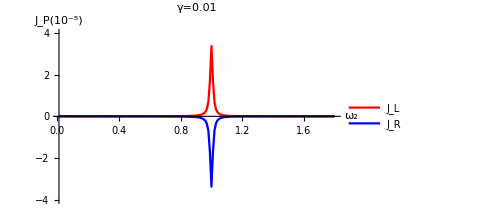
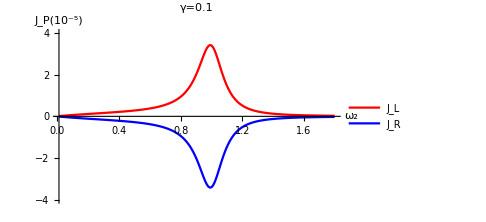
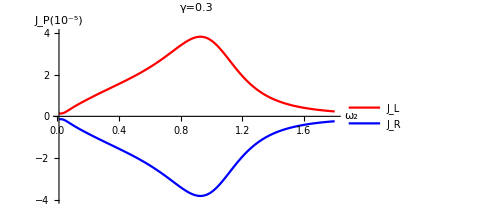

```mathematica
{
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.01ωconv;
ω1=1.0ωconv;
ω2min=0.01ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres,True,"γ=0.01"]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.1ωconv;
ω1=1.0ωconv;
ω2min=0.01ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres,True,"γ=0.1"]
],
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γs=0.3ωconv;
ω1=1.0ωconv;
ω2min=0.01ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γs,ωres,True,"γ=0.3"]
]
}
```

### Energy flow under different levels of resonance and different coupling strengths

```mathematica
PlotEngyFlowsWithω2andγ[T1_,T2_,κ1_,κ2_,ω1s_,ω2min_,ω2max_,γmin_,γmax_,ωres_,γres_,legends_]:=Module[{tempx,tempy,tempz,temp},
tempx=Table[ω2,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempy=Table[γ,{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
tempz=10^5 Table[varFunc[T1,T2,κ1,κ2,ω1s,ω2,γ,unitassum][[3,1]],{ω2,ω2min,ω2max,ωres},{γ,γmin,γmax,γres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
Show[
ListPlot3D[temp,
	PlotRange->{{ω2min,ω2max},{γmin,γmax},Full},
	ImageSize->Large,
	AxesStyle->Directive[Darker[Gray],18.5,FontFamily->"Times New Roman"],
	AxesLabel->{
		Style["ω_2/Δ",FontFamily->"Times New Roman",FontSize->19.5],
		Style["γ/Δ",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"BlueGreenYellow"],
Graphics3D[Text[Style["10^-5J_1/ℏΔ^2",Darker[Gray],FontFamily->"Times New Roman",FontSize->19.5],Scaled[{0.13,0.03,0.72}]]]
]
]
```

```mathematica
Module[{T1,T2,κ1,κ2,ω1,ω2min,ω2max,γmin,γmax,ωres,γres},
T1=0.2Tconv;T2=0.02Tconv;
κ1=0.01;κ2=0.01;
γmin=0.03ωconv;γmax=0.3 ωconv;γres=0.005;
ω1=1.0ωconv;
ω2min=0.1ωconv;ω2max=1.8ωconv;ωres=0.01ωconv;
PlotEngyFlowsWithω2andγ[T1,T2,κ1,κ2,ω1,ω2min,ω2max,γmin,γmax,ωres,γres,True]
]
```

-Graphics3D-